## Importing data all

```mathematica
Quit
```

```mathematica
SetDirectory[$UserDocumentsDirectory]
```

/home/drigo/Documents

```mathematica
Get["datasets2016.mx"]
```

```mathematica
Get["aGENCY2016.mx"]
```

```mathematica
Get["categorieS2016.mx"]
```

```mathematica
Get["datasets2015.mx"]
```

```mathematica
Get["aGENCY2015.mx"]
```

```mathematica
Get["categorieS2015.mx"]
```

```mathematica
Get["datasets2014.mx"]
```

```mathematica
Get["aGENCY2014.mx"]
```

```mathematica
Get["categorieS2014.mx"]
```

```mathematica
Get["datasets2013.mx"]
```

```mathematica
Get["aGENCY2013.mx"]
```

```mathematica
Get["categorieS2013.mx"]
```

```mathematica
dataAlltogether2016=Flatten@Values[datasetsCS2016];
dataAlltogether2015=Flatten@Values[datasetsCS2015];
dataAlltogether2014=Flatten@Values[datasetsCS2014];
dataAlltogether2013=Flatten@Values[datasetsCS2013];
```

```mathematica
coutr2016=DeleteDuplicates[Table[dataAlltogether2016[[i]][["BenefitingLocation"]],{i,1,Length[dataAlltogether2016]}]];
coutr2015=DeleteDuplicates[Table[dataAlltogether2015[[i]][["BenefitingLocation"]],{i,1,Length[dataAlltogether2015]}]];
coutr2014=DeleteDuplicates[Table[dataAlltogether2014[[i]][["BenefitingLocation"]],{i,1,Length[dataAlltogether2014]}]];
coutr2013=DeleteDuplicates[Table[dataAlltogether2013[[i]][["BenefitingLocation"]],{i,1,Length[dataAlltogether2013]}]];
```

```mathematica
{Length[coutr2016],Length[coutr2015],Length[coutr2014],Length[coutr2013]}
```

{136,142,132,136}

```mathematica
Complement[coutr2015,coutr2016]
```

{Bhutan,Denmark,Dominica,Ireland,Italy,Kiribati,Singapore,Suriname,Switzerland,Tuvalu}

```mathematica
Complement[coutr2014,coutr2016]
```

{Bhutan,Denmark,Ireland,Italy,Malta,Suriname,Switzerland}

```mathematica
Complement[coutr2013,coutr2016]
```

{Denmark,France,Germany,Ireland,Italy,Malta,Suriname,Switzerland}

```mathematica
Intersection[coutr2013,coutr2014,coutr2015,coutr2016]
```

{Afghanistan,Albania,Algeria,Angola,Argentina,Armenia,Azerbaijan,Bahamas, The,Bangladesh,Barbados,Belarus,Belize,Benin,Bolivia,Botswana,Brazil,Brunei,Bulgaria,Burundi,Cambodia,Cameroon,Chad,Chile,China,Colombia,Comoros,Croatia,Cuba,Cyprus,Djibouti,Dominican Republic,Ecuador,Egypt,Eritrea,Estonia,Ethiopia,Fiji,Gabon,Gambia, The,Georgia,Ghana,Guatemala,Guinea,Guinea-Bissau,Guyana,Haiti,Honduras,Hungary,India,Indonesia,Iraq,Israel,Jamaica,Japan,Jordan,Kazakhstan,Kenya,Kosovo,Kyrgyzstan,Laos,Lebanon,Lesotho,Liberia,Libya,Lithuania,Macedonia,Madagascar,Malawi,Malaysia,Maldives,Mali,Mauritania,Mauritius,Mexico,Micronesia, Federated States of,Moldova,Mongolia,Montenegro,Morocco,Mozambique,Namibia,Nepal,Nicaragua,Niger,Nigeria,Pakistan,Panama,Papua New Guinea,Paraguay,Peru,Philippines,Romania,Russia,Rwanda,Samoa,Senegal,Serbia,Seychelles,Slovakia,Somalia,South Sudan,Sudan,Swaziland,Syria,Tajikistan,Tanzania,Thailand,Togo,Tonga,Tunisia,Turkey,Turkmenistan,Uganda,Ukraine,Uruguay,Uzbekistan,Vanuatu,Venezuela,Vietnam,Yemen,Zambia,Zimbabwe}

```mathematica
(*Join[dataAlltogether2016,dataAlltogether2015,dataAlltogether2014,dataAlltogether2013]*)
```

```mathematica
datasetAll201316d1=Join[dataAlltogether2016,dataAlltogether2015,dataAlltogether2014,dataAlltogether2013];
```

```mathematica
(*datasetAll201316d1[[All,"Amount"]]*)
```

Checking if the all lines (associations) have the same columns:

```mathematica
datasetAll201316d1key=DeleteDuplicates[Keys[Join[dataAlltogether2016,dataAlltogether2015,dataAlltogether2014,dataAlltogether2013]]]
```

{{AgencyName,Amount,Category,Year,BenefitingLocation,Sector}}

```mathematica
Clear[AnalysisAmountNew1]
```

```mathematica
AnalysisAmountNew1=MapAt[Interpreter[Restricted["StructuredQuantity","USDollars"]],datasetAll201316d1,{1;;,2}];
```

```mathematica
(*AnalysisAmountNew1[[1;;2]]//InputForm*)
```

Categories

```mathematica
{DeleteDuplicates[datasetAll201316d1[[All,"Category"]]]//TableForm,Length[DeleteDuplicates[datasetAll201316d1[[All,"Category"]]]]}
```

{Economic Development
Peace and Security
Program Management
Multi-sector
Education and Social Services
Democracy, Human Rights, and Governance
Humanitarian Assistance
Health
Environment,9}

Agencies

```mathematica
{DeleteDuplicates[datasetAll201316d1[[All,"AgencyName"]]]//TableForm,Length[DeleteDuplicates[datasetAll201316d1[[All,"AgencyName"]]]]}
```

{Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services,14}

```mathematica
AnalysisAmountNew1
```

{<|AgencyName→Overseas Private Investment Corporation,Amount→2.e7 $,Category→Economic Development,Year→2016,BenefitingLocation→Jordan,Sector→Financial Sector|>,<|AgencyName→Department of Defense,Amount→1.5235e7 $,Category→Peace and Security,Year→2016,BenefitingLocation→Jordan,Sector→Combating Weapons of Mass Destruction (WMD)|>,145514,<|AgencyName→Department of Health and Human Services,Amount→64 181.16 $,Category→Health,Year→2013,BenefitingLocation→Zimbabwe,Sector→Pandemic Influenza and Other Emerging Threats (PIOET)|>,<|AgencyName→Department of Health and Human Services,Amount→34 570.84 $,Category→Health,Year→2013,BenefitingLocation→Zimbabwe,Sector→Pandemic Influenza and Other Emerging Threats (PIOET)|>}
 |  |  |  |

```mathematica
AnalysisAmountNewOhneZero1=DeleteCases[AnalysisAmountNew1[[;;All]],x_?(QuantityMagnitude[#Amount]==0&)];
```

```mathematica
Dataset[AnalysisAmountNewOhneZero1]
```

Dataset[<>]

```mathematica
countryAnalysisNew[category_,year_,agencyName_,country_]:=With[{r=Select[Select[Select[Select[AnalysisAmountNewOhneZero1,#[[3]]==category&],#[[4]]==year&],#[[1]]==agencyName&],#[[5]]==country&]},If[Length[r]==0,{Association[Rule["AgencyName",""],Rule["Amount","0.00"],Rule["Category",""],Rule["Year",""],Rule["BenefitingLocation",""],Rule["Sector",""]]},r]];
```

```mathematica
countryAnalysisNew["Economic Development","2015","Peace Corps","Peru"][[1;;,2]]//Dataset
```

Dataset[<>]

```mathematica
COUNTRYAnalysisAmountNew[category_,year_,agencyName_,country_]:=MapAt[Interpreter[Restricted["StructuredQuantity","USDollars"]],countryAnalysisNew[category,year,agencyName,country],{1;;,2}];
```

```mathematica
countryAnalysisTotUSDollarNew[category_,year_,agencyName_,country_]:=Total[COUNTRYAnalysisAmountNew[category,year,agencyName,country][[All,"Amount"]]];
```

```mathematica
countryAnalysisTotUSDollarNew["Economic Development","2015","Peace Corps","Peru"]
```

12 678.31 $

```mathematica
countryAnalysisTotUSDollarNew["Economic Development","2016","Peace Corps","Peru"]
```

1.081918e6 $

```mathematica
dtotcountry[category_,agency_,country_]:=Map[agency->{#,countryAnalysisTotUSDollarNew[category,ToString[#],agency,country]}&,Range[2013,2016]]
```

```mathematica
dtotcountry["Economic Development","Peace Corps","Peru"]
```

{Peace Corps→{2013,679 433.86 $},Peace Corps→{2014,786 447.03 $},Peace Corps→{2015,12 678.31 $},Peace Corps→{2016,1.081918e6 $}}

```mathematica
dtotlistCountryNew[category_,country_]:=Map[dtotcountry[category,#,country]&,DeleteDuplicates[datasetAll201316d1[[All,"AgencyName"]]]];
```

```mathematica
(*dtotlistCountryNew["Economic Development","Peru"]//TableForm*)
```

```mathematica
(*Values[dtotlistCountryNew["Economic Development","Peru"]][[11]]//TableForm*)
```

```mathematica
(*Keys[dtotlistCountryNew["Economic Development","Peru"]][[All,1]]//TableForm*)
```

#### List-log-plot

```mathematica
frameticksLogplot={{{{10^4,"10^4"},{10^5,"10^5"},{10^6,"10^6"},{10^7,"10^7"},{10^8,"10^8"}},None},{{2013,2014,2015,2016},None}};
```

```mathematica
lpOverseasCountry[category_,country_]:=ListLogPlot[Values[dtotlistCountryNew[category,country]][[1]],PlotRange->{All,All},PlotLegends->{"Overseas Private Investment Corporation"},Frame->True,FrameLabel->{"Year",$ },FrameTicks->frameticksLogplot,PlotStyle->{PointSize[Large],Black},FrameTicks->frameticksLogplot,PlotLabel->category];
```

```mathematica
lpDefenseCountry[category_,country_]:=ListLogPlot[Values[dtotlistCountryNew[category,country]][[2]],PlotRange->{All,All},PlotLegends->{"Department of Defence"},Frame->True,FrameLabel->{"Year",$ },PlotStyle->{PointSize[Large],RGBColor[.5,.8,.1]},FrameTicks->frameticksLogplot,PlotLabel->category]
```

```mathematica
lpPeaceCountry[category_,country_]:=ListLogPlot[Values[dtotlistCountryNew[category,country]][[3]], PlotRange -> {All, All}, PlotLegends -> {"Peace Corps"}, Frame -> True, FrameLabel -> {"Years", $ }, PlotStyle -> {PointSize[Large], Pink},FrameTicks->frameticksLogplot, PlotLabel -> category]
```

```mathematica
lpInternDevelopCountry[category_,country_]:=ListLogPlot[Values[dtotlistCountryNew[category,country]][[4]],PlotRange->{All,All},PlotLegends->{"U.S. Agency for International Development"},Frame->True,FrameLabel->{"Year",$ },FrameTicks->frameticksLogplot,PlotStyle->{PointSize[Large],Blue},PlotLabel->category]
```

```mathematica
lpDepartStateCountry[category_,country_]:=ListLogPlot[Values[dtotlistCountryNew[category,country]][[5]],PlotRange->{All,All},PlotLegends->{"U.S. Department of State"},Frame->True,FrameLabel->{"Year",$ },PlotStyle->{PointSize[Large],Orange},FrameTicks->frameticksLogplot,PlotLabel->category]
```

```mathematica
lpTreasuryCountry[category_,country_]:=ListLogPlot[Values[dtotlistCountryNew[category,country]][[6]], PlotRange -> {All, All}, PlotLegends -> {"U.S. Department of the Treasury"}, Frame -> True, FrameLabel -> {"Year", $ }, PlotStyle -> {PointSize[Large],Lighter[Purple,0.58]},FrameTicks->frameticksLogplot, PlotLabel -> category]
```

```mathematica
lpInterAmericanCountry[category_,country_]:=ListLogPlot[Values[dtotlistCountryNew[category,country]][[7]],PlotRange->{All,All},PlotLegends->{"Inter-American Foundation"},Frame->True,FrameLabel->{"Year",$ },FrameTicks->frameticksLogplot,PlotStyle->{PointSize[Large],Lighter[Green,0.08]},PlotLabel->category]
```

```mathematica
lpInteriorCountry[category_,country_]:=ListLogPlot[Values[dtotlistCountryNew[category,country]][[8]],PlotRange->{All,All},PlotLegends->{"Department of Interior"},Frame->True,FrameLabel->{"Year",$ },PlotStyle->{PointSize[Large],RGBColor[.2,.95,.7]},PlotLabel->category]
```

```mathematica
lpAfricaCountry[category_,country_]:=ListLogPlot[Values[dtotlistCountryNew[category,country]][[9]],PlotRange->{All,All},PlotLegends->{"U.S. African Development Foundation"},Frame->True,FrameLabel->{"Year",$ },FrameTicks->frameticksLogplot,PlotStyle->{PointSize[Large],RGBColor[.2,.95,.7]},PlotLabel->category]
```

```mathematica
lpJusticeCountry[category_,country_]:=ListLogPlot[Values[dtotlistCountryNew[category,country]][[10]],PlotRange->{All,All},PlotLegends->{"Department of Justice"},Frame->True,FrameLabel->{"Years",$ },PlotStyle->{PointSize[Large],Magenta},FrameTicks->frameticksLogplot,PlotLabel->category]
```

```mathematica
lpLaborCountry[category_,country_]:=ListLogPlot[Values[dtotlistCountryNew[category,country]][[11]],PlotRange->{All,All},PlotLegends->{"Department of Labor"},Frame->True,FrameLabel->{"Years",$ },PlotStyle->{PointSize[Large],RGBColor[.25,.75,.78]},FrameTicks->frameticksLogplot,PlotLabel->category]
```

```mathematica
lpAgricultureCountry[category_,country_]:=ListLogPlot[Values[dtotlistCountryNew[category,country]][[12]],PlotRange->{All,All},PlotLegends->{"U.S. Department of Agriculture"},Frame->True,FrameLabel->{"Year",$ },PlotStyle->{PointSize[Large],RGBColor[.25,.75,.78]},FrameTicks->frameticksLogplot,PlotLabel->category]
```

```mathematica
lpMillenniumnCountry[category_,country_]:=ListLogPlot[Values[dtotlistCountryNew[category,country]][[13]],PlotRange->{All,All},PlotLegends->{"Millennium Challenge Corporation"},FrameTicks->frameticksLogplot,Frame->True,FrameLabel->{"Year",$ },PlotStyle->{PointSize[Large],RGBColor[.15,.55,.78]},PlotLabel->category]
```

```mathematica
lpHumanServicesCountry[category_,country_]:=ListLogPlot[Values[dtotlistCountryNew[category,country]][[14]],PlotRange->{All,All},PlotLegends->{"Department of Health and Human Services"},Frame->True,FrameTicks->frameticksLogplot,FrameLabel->{"Year",$ },PlotStyle->{PointSize[Large],RGBColor[0.89,0.78,0.17]},PlotLabel->{"Department of Health and Human Services"}]
```

```mathematica
(*lpTreasuryCountry["Economic Development","Peru"]*)
```

```mathematica
(*lpLaborCountry["Economic Development","Peru"];*)
```

## Peru - Data (2013 - 2016) - categories

```mathematica
TableForm[DeleteDuplicates[datasetAll201316d1[[All,"Category"]]]]
```

Economic Development
Peace and Security
Program Management
Multi-sector
Education and Social Services
Democracy, Human Rights, and Governance
Humanitarian Assistance
Health
Environment

### Economic Development*

```mathematica
dtotlistCountryNew["Economic Development","Peru"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Economic Development","Peru"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
90 000.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
679 433.86 $ | 2014
786 447.03 $ | 2015
12 678.31 $ | 2016
1.081918e6 $
2013
2.71988212e6 $ | 2014
-250 766.98 $ | 2015
244 045.10 $ | 2016
413 320.71 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
307 553.66 $ | 2014
435 734.97 $ | 2015
310 494.57 $ | 2016
268 964.70 $
2013
0.00 $ | 2014
807 450.00 $ | 2015
1.04723195e6 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
1.e6 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Economic Development","Peru"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

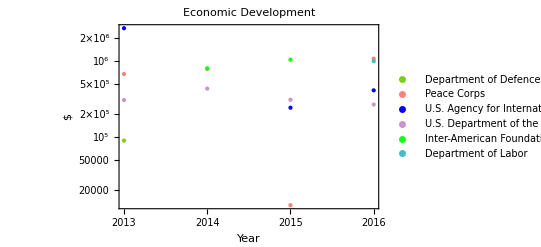

```mathematica
Show[lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2003,Log[5*10^3]}]
```

### Peace and Security*

```mathematica
dtotlistCountryNew["Peace and Security","Peru"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Peace and Security","Peru"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
4.965e6 $ | 2014
4.52e6 $ | 2015
6.487e6 $ | 2016
1.5521e7 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
2.803557112e7 $ | 2014
3.1733775e7 $ | 2015
1.850041598e7 $ | 2016
1.900996856e7 $
2013
2.889717e6 $ | 2014
4.64698066e6 $ | 2015
4.28994199e6 $ | 2016
-132 434.26 $
2013
0.00 $ | 2014
550 679.55 $ | 2015
265 403.35 $ | 2016
184 186.18 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
228 596.61 $ | 2016
16 420.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Peace and Security","Peru"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

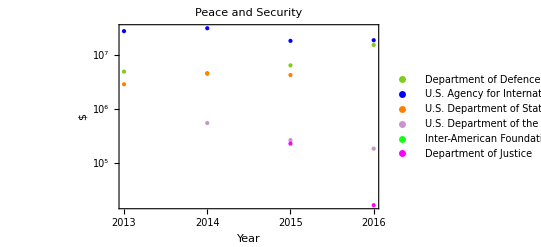

```mathematica
Show[lpDefenseCountry["Peace and Security","Peru"],lpInternDevelopCountry["Peace and Security","Peru"],lpDepartStateCountry["Peace and Security","Peru"],lpTreasuryCountry["Peace and Security","Peru"],lpInterAmericanCountry["Peace and Security","Peru"],lpJusticeCountry["Peace and Security","Peru"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}]
```

### Program Management*

```mathematica
dtotlistCountryNew["Program Management","Peru"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Program Management","Peru"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
7.444131210000001e6 $ | 2014
9.19964341e6 $ | 2015
7.81939126e6 $ | 2016
6.22201625e6 $
2013
1.5703836400000001e6 $ | 2014
1.8365468900000001e6 $ | 2015
-503.99 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
171 673.10 $
2013
85 000.00 $ | 2014
170 325.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Program Management","Peru"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

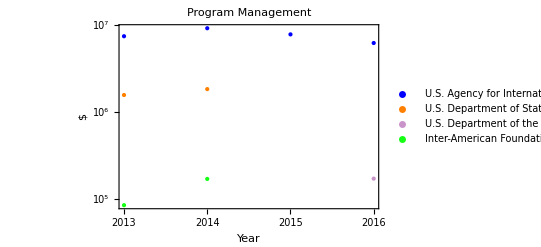

```mathematica
Show[lpInternDevelopCountry["Program Management","Peru"],lpDepartStateCountry["Program Management","Peru"],lpTreasuryCountry["Program Management","Peru"],lpInterAmericanCountry["Program Management","Peru"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}]
```

### Multi-sector*

```mathematica
dtotlistCountryNew["Multi-sector","Peru"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Multi-sector","Peru"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
5.e6 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
78 995.17 $ | 2014
82 589.10 $ | 2015
37 547.45 $ | 2016
111 240.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
88 457.60 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Multi-sector","Peru"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

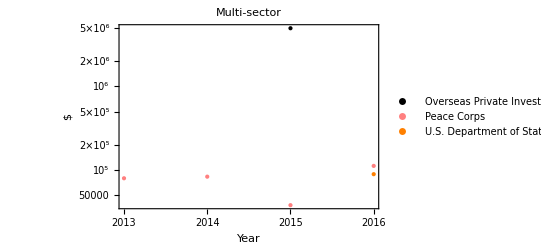

```mathematica
Show[lpOverseasCountry["Multi-sector","Peru"],lpPeaceCountry["Multi-sector","Peru"],lpDepartStateCountry["Multi-sector","Peru"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}]
```

### Education and Social Services*

```mathematica
dtotlistCountryNew["Education and Social Services","Peru"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Education and Social Services","Peru"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
14 999.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
1.4595924200000002e6 $ | 2014
1.53512683e6 $ | 2015
0.00 $ | 2016
1.165982e6 $
2013
3.72936241e6 $ | 2014
3.9513615300000003e6 $ | 2015
5.30982971e6 $ | 2016
5.14946678e6 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
699 474.00 $ | 2015
152 187.16 $ | 2016
872 975.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Education and Social Services","Peru"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

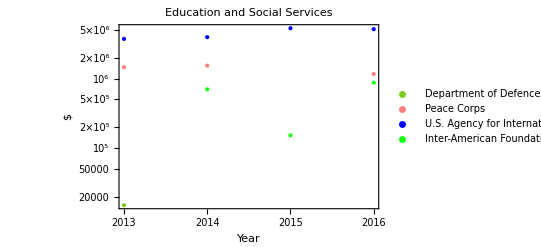

```mathematica
Show[lpDefenseCountry["Education and Social Services","Peru"],lpPeaceCountry["Education and Social Services","Peru"],lpInternDevelopCountry["Education and Social Services","Peru"],lpInterAmericanCountry["Education and Social Services","Peru"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}]
```

### Democracy, Human Rights, and Governance*

```mathematica
dtotlistCountryNew["Democracy, Human Rights, and Governance","Peru"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Democracy, Human Rights, and Governance","Peru"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
4.468626890000001e6 $ | 2014
4.83964845e6 $ | 2015
4.22298063e6 $ | 2016
2.15028687e6 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
249 517.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Democracy, Human Rights, and Governance","Peru"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

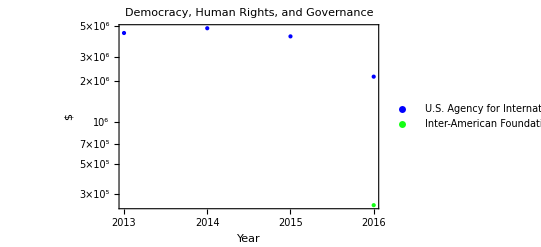

```mathematica
Show[lpInternDevelopCountry["Democracy, Human Rights, and Governance","Peru"],lpInterAmericanCountry["Democracy, Human Rights, and Governance","Peru"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}]
```

### Humanitarian Assistance*

```mathematica
dtotlistCountryNew["Humanitarian Assistance","Peru"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Humanitarian Assistance","Peru"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
6.712e6 $ | 2014
0.00 $ | 2015
15 000.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
281 706.00 $ | 2014
4.71090384e6 $ | 2015
402 304.00 $ | 2016
1.514546e6 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Humanitarian Assistance","Peru"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

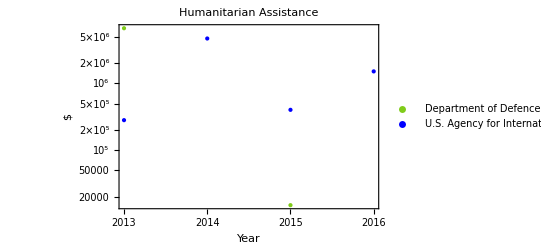

```mathematica
Show[lpDefenseCountry["Humanitarian Assistance","Peru"],lpInternDevelopCountry["Humanitarian Assistance","Peru"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}]
```

### Health*

```mathematica
dtotlistCountryNew["Health","Peru"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Health","Peru"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
363 320.00 $ | 2014
275 000.00 $ | 2015
255 000.00 $ | 2016
270 000.00 $
2013
2.0116453199999998e6 $ | 2014
2.29883605e6 $ | 2015
-1 135.63 $ | 2016
2.385265e6 $
2013
8.052862210000001e6 $ | 2014
2.50387434e6 $ | 2015
2.5956359399999995e6 $ | 2016
405 662.79 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
114 878.00 $ | 2014
205 541.62 $ | 2015
15 168.33 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Health","Peru"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

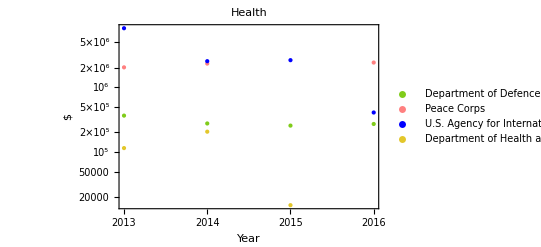

```mathematica
Show[lpDefenseCountry["Health","Peru"],lpPeaceCountry["Health","Peru"],lpInternDevelopCountry["Health","Peru"],lpHumanServicesCountry["Health","Peru"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}]
```

### Environment*

```mathematica
dtotlistCountryNew["Environment","Peru"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Environment","Peru"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
879 301.13 $ | 2014
901 660.73 $ | 2015
5.832197e6 $ | 2016
1.008298e6 $
2013
1.9541619439999998e7 $ | 2014
1.334872831e7 $ | 2015
2.134906613e7 $ | 2016
1.397225415e7 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
75 880.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
84 457.00 $ | 2016
369 239.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Environment","Peru"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

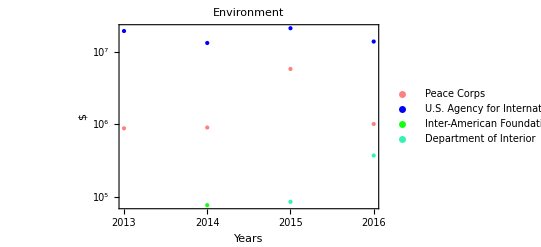

```mathematica
Show[lpPeaceCountry["Environment","Peru"],lpInternDevelopCountry["Environment","Peru"],lpInterAmericanCountry["Environment","Peru"],lpInteriorCountry["Environment","Peru"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}]
```

## Jordan - Data (2013 - 2016) - categories

```mathematica
TableForm[DeleteDuplicates[datasetAll201316d1[[All,"Category"]]]]
```

Economic Development
Peace and Security
Program Management
Multi-sector
Education and Social Services
Democracy, Human Rights, and Governance
Humanitarian Assistance
Health
Environment

### Economic Development*

```mathematica
dtotlistCountryNew["Economic Development","Jordan"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Economic Development","Jordan"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
1.23331e7 $ | 2016
2.e7 $
2013
456 000.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
3 505.89 $ | 2016
0.00 $
2013
4.3932362983e8 $ | 2014
4.1222044543000007e8 $ | 2015
6.4929823789e8 $ | 2016
3.0277335835999995e8 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
77 862.40 $ | 2016
15 971.80 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
2.51e7 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Economic Development","Jordan"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

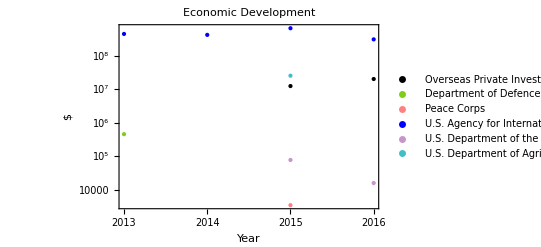

```mathematica
Show[lpOverseasCountry["Economic Development","Jordan"],lpDefenseCountry["Economic Development","Jordan"],lpPeaceCountry["Economic Development","Jordan"],lpInternDevelopCountry["Economic Development","Jordan"],lpTreasuryCountry["Economic Development","Jordan"],lpAgricultureCountry["Economic Development","Jordan"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2003,Log[5*10^3]}]
```

### Peace and Security*

```mathematica
dtotlistCountryNew["Peace and Security","Jordan"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Peace and Security","Jordan"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
4.2023159629999995e7 $ | 2015
7.900736967999999e7 $ | 2016
1.5235e7 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
1.999999e6 $ | 2015
-806 000.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Peace and Security","Jordan"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

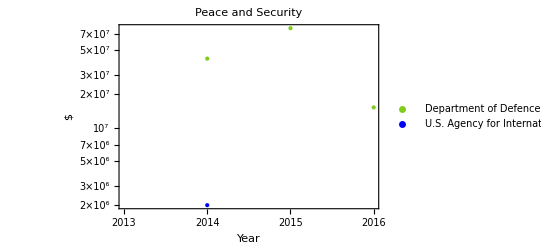

```mathematica
Show[lpDefenseCountry["Peace and Security","Jordan"],lpInternDevelopCountry["Peace and Security","Jordan"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}]
```

### Program Management*

```mathematica
dtotlistCountryNew["Program Management","Jordan"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Program Management","Jordan"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
264 436.00 $
2013
5.9575448e6 $ | 2014
8.922153329999998e6 $ | 2015
1.043628454e7 $ | 2016
1.004700979e7 $
2013
35 895.76 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
-1.84196147e6 $ | 2014
2.90859158e6 $ | 2015
-625.72 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Program Management","Jordan"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

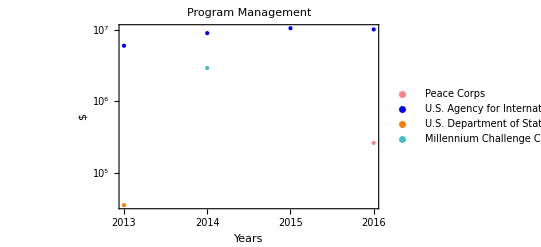

```mathematica
Show[lpPeaceCountry["Program Management","Jordan"],lpInternDevelopCountry["Program Management","Jordan"],lpDepartStateCountry["Program Management","Jordan"],lpMillenniumnCountry["Program Management","Jordan"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}]
```

### Multi-sector*

```mathematica
dtotlistCountryNew["Multi-sector","Jordan"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Multi-sector","Jordan"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
97 629.09 $ | 2014
93 276.84 $ | 2015
43 839.28 $ | 2016
9 502.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
832 573.15 $ | 2014
67 916.00 $ | 2015
-95 683.97 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
1.81943238e6 $ | 2014
800 880.28 $ | 2015
687 299.90 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Multi-sector","Jordan"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

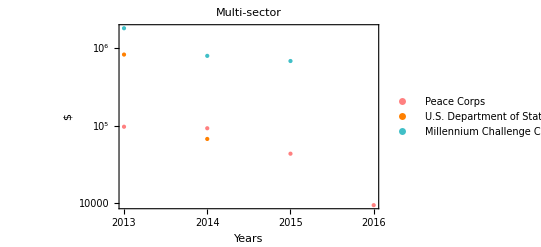

```mathematica
Show[lpPeaceCountry["Multi-sector","Jordan"],lpDepartStateCountry["Multi-sector","Jordan"],lpMillenniumnCountry["Multi-sector","Jordan"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}]
```

### Education and Social Services*

```mathematica
dtotlistCountryNew["Education and Social Services","Jordan"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Education and Social Services","Jordan"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
1.0951410499999998e6 $ | 2014
1.16639958e6 $ | 2015
0.00 $ | 2016
2.00 $
2013
4.800269795e7 $ | 2014
3.2009372919999998e7 $ | 2015
3.6274373050000004e7 $ | 2016
7.194973738999999e7 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Education and Social Services","Jordan"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

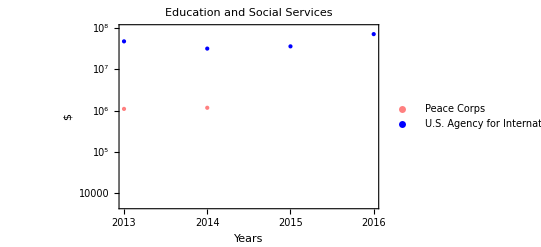

```mathematica
Show[lpPeaceCountry["Education and Social Services","Jordan"],lpInternDevelopCountry["Education and Social Services","Jordan"],PlotRange->{{2013,2016},{Log[5*10^3],Log[10^8]}},AxesOrigin->{2009,Log[8*10^1]}]
```

### Democracy, Human Rights, and Governance*

```mathematica
dtotlistCountryNew["Democracy, Human Rights, and Governance","Jordan"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Democracy, Human Rights, and Governance","Jordan"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
2.134411734e7 $ | 2014
2.129860725e7 $ | 2015
2.54558915e7 $ | 2016
3.881874604e7 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Democracy, Human Rights, and Governance","Jordan"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

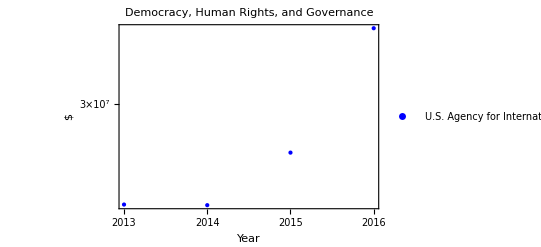

```mathematica
Show[lpInternDevelopCountry["Democracy, Human Rights, and Governance","Jordan"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}]
```

### Humanitarian Assistance*

```mathematica
dtotlistCountryNew["Humanitarian Assistance","Jordan"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Humanitarian Assistance","Jordan"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
2.1e6 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
1.2112941639e8 $ | 2014
2.7314248854e8 $ | 2015
2.4611955104e8 $ | 2016
129 436.95 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Humanitarian Assistance","Jordan"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

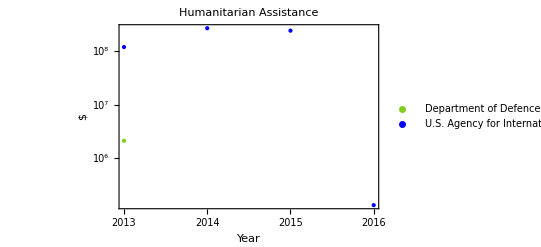

```mathematica
Show[lpDefenseCountry["Humanitarian Assistance","Jordan"],lpInternDevelopCountry["Humanitarian Assistance","Jordan"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}]
```

### Health*

```mathematica
dtotlistCountryNew["Health","Jordan"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Health","Jordan"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
2.322e6 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
225 855.15 $ | 2014
88 363.58 $ | 2015
0.00 $ | 2016
0.00 $
2013
3.7483499129999995e7 $ | 2014
3.942841139e7 $ | 2015
5.4607208410000004e7 $ | 2016
5.28086067e7 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
961 961.47 $ | 2014
-2.90859158e6 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
224 466.78 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Health","Jordan"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

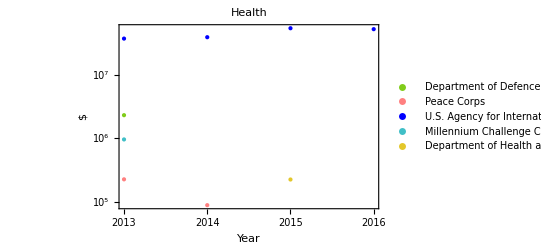

```mathematica
Show[lpDefenseCountry["Health","Jordan"],lpPeaceCountry["Health","Jordan"],lpInternDevelopCountry["Health","Jordan"],lpMillenniumnCountry["Health","Jordan"],lpHumanServicesCountry["Health","Jordan"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}]
```

### Environment*

```mathematica
dtotlistCountryNew["Environment","Jordan"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Environment","Jordan"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
1.13992512e6 $ | 2016
0.00 $
2013
1.1117771120000001e7 $ | 2014
1.98716162e6 $ | 2015
1.9483833399999999e6 $ | 2016
1.4955587e6 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Environment","Jordan"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

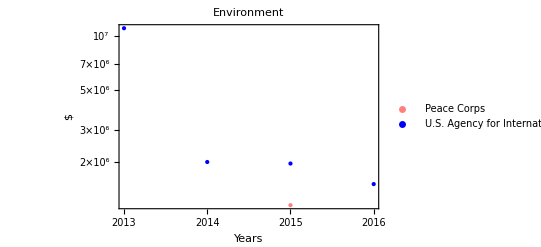

```mathematica
Show[lpPeaceCountry["Environment","Jordan"],lpInternDevelopCountry["Environment","Jordan"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}]
```

## Tanzania - Data (2013 - 2016) - categories

```mathematica
TableForm[DeleteDuplicates[datasetAll201316d1[[All,"Category"]]]]
```

Economic Development
Peace and Security
Program Management
Multi-sector
Education and Social Services
Democracy, Human Rights, and Governance
Humanitarian Assistance
Health
Environment

### Economic Development*

```mathematica
dtotlistCountryNew["Economic Development","Tanzania"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Economic Development","Tanzania"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
2.e7 $ | 2016
1.5e7 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
19 747.98 $ | 2014
69 070.04 $ | 2015
122 023.81 $ | 2016
139 977.00 $
2013
4.224798954e7 $ | 2014
9.400722534e7 $ | 2015
3.303152223e7 $ | 2016
4.834308706e7 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
693 348.13 $ | 2014
672 445.47 $ | 2015
1.10994896e6 $ | 2016
888 033.79 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
239 022.00 $ | 2014
1.056463e6 $ | 2015
821 713.00 $ | 2016
980 506.97 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
2.02e7 $ | 2015
0.00 $ | 2016
0.00 $
2013
2.11757844e7 $ | 2014
6.643384800000001e6 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Economic Development","Tanzania"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

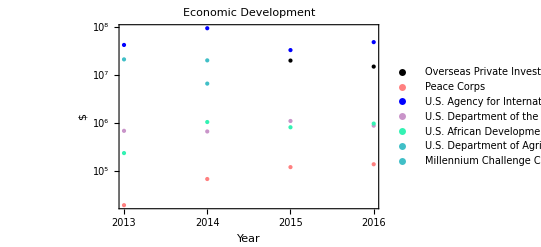

```mathematica
Show[lpOverseasCountry["Economic Development","Tanzania"],lpPeaceCountry["Economic Development","Tanzania"],lpInternDevelopCountry["Economic Development","Tanzania"],lpTreasuryCountry["Economic Development","Tanzania"],lpAfricaCountry["Economic Development","Tanzania"],lpAgricultureCountry["Economic Development","Tanzania"],lpMillenniumnCountry["Economic Development","Tanzania"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2003,Log[5*10^3]}]
```

### Peace and Security*

```mathematica
dtotlistCountryNew["Peace and Security","Tanzania"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Peace and Security","Tanzania"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
214 000.00 $ | 2014
5.97439e6 $ | 2015
3.45613887e6 $ | 2016
246 000.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
400 000.00 $ | 2014
448 000.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
-5 354.90 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Peace and Security","Tanzania"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

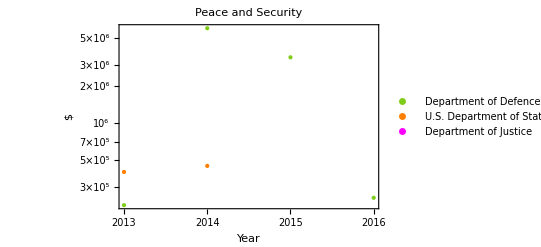

```mathematica
Show[lpDefenseCountry["Peace and Security","Tanzania"],lpDepartStateCountry["Peace and Security","Tanzania"],lpJusticeCountry["Peace and Security","Tanzania"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}]
```

### Program Management*

```mathematica
dtotlistCountryNew["Program Management","Tanzania"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Program Management","Tanzania"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
7.107666890000001e6 $ | 2014
1.135783468e7 $ | 2015
1.182241339e7 $ | 2016
1.169088128e7 $
2013
18 158.50 $ | 2014
-28.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
9 157.43 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
231 710.00 $ | 2014
115 793.00 $ | 2015
567 648.00 $ | 2016
566 401.09 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
-1.566093744e7 $ | 2014
-4.2690219e6 $ | 2015
1.48e6 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Program Management","Tanzania"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

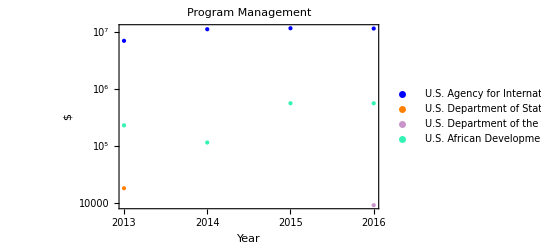

```mathematica
Show[lpInternDevelopCountry["Program Management","Tanzania"],lpDepartStateCountry["Program Management","Tanzania"],lpTreasuryCountry["Program Management","Tanzania"],lpAfricaCountry["Program Management","Tanzania"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}](*lpMillenniumnCountry["Program Management","Tanzania"]*)
```

### Multi-sector*

```mathematica
dtotlistCountryNew["Multi-sector","Tanzania"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Multi-sector","Tanzania"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
21 025.80 $ | 2014
39 807.30 $ | 2015
88 027.87 $ | 2016
38 991.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
1.73788208e6 $ | 2014
2.4074562800000003e6 $ | 2015
9.73398924e6 $ | 2016
0.00 $
2013
0.00 $ | 2014
47 705.03 $ | 2015
185 606.28 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Multi-sector","Tanzania"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

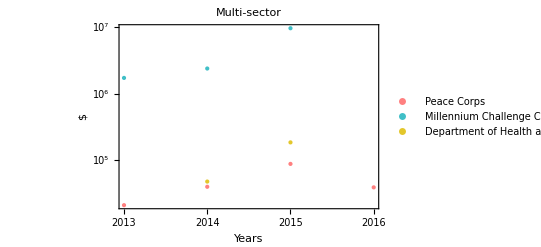

```mathematica
Show[lpPeaceCountry["Multi-sector","Tanzania"],lpMillenniumnCountry["Multi-sector","Tanzania"],lpHumanServicesCountry["Multi-sector","Tanzania"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}]
```

### Education and Social Services*

```mathematica
dtotlistCountryNew["Education and Social Services","Tanzania"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Education and Social Services","Tanzania"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
1.67355829e6 $ | 2014
2.45818512e6 $ | 2015
0.00 $ | 2016
2.912345e6 $
2013
7.904964649999999e6 $ | 2014
1.5839360969999999e7 $ | 2015
1.204167979e7 $ | 2016
1.902999051e7 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
5.151570613e7 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Education and Social Services","Tanzania"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

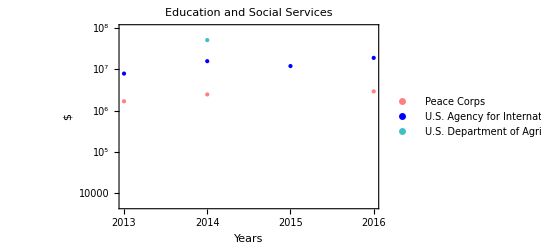

```mathematica
Show[lpPeaceCountry["Education and Social Services","Tanzania"],lpInternDevelopCountry["Education and Social Services","Tanzania"],lpAgricultureCountry["Education and Social Services","Tanzania"],PlotRange->{{2013,2016},{Log[5*10^3],Log[10^8]}},AxesOrigin->{2009,Log[8*10^1]}]
```

### Democracy, Human Rights, and Governance*

```mathematica
dtotlistCountryNew["Democracy, Human Rights, and Governance","Tanzania"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Democracy, Human Rights, and Governance","Tanzania"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
7.96288542e6 $ | 2014
5.78541e6 $ | 2015
9.254075389999999e6 $ | 2016
3.e6 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Democracy, Human Rights, and Governance","Tanzania"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

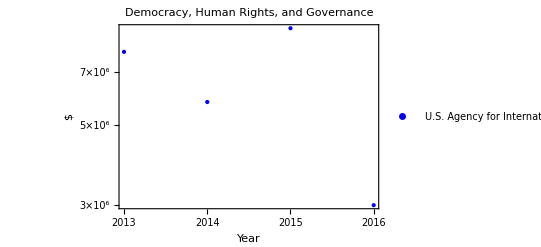

```mathematica
Show[lpInternDevelopCountry["Democracy, Human Rights, and Governance","Tanzania"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}]
```

### Humanitarian Assistance*

```mathematica
dtotlistCountryNew["Humanitarian Assistance","Tanzania"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Humanitarian Assistance","Tanzania"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
274 818.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
2.964268e6 $ | 2014
3.9999e6 $ | 2015
1.260662e6 $ | 2016
277 156.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Humanitarian Assistance","Tanzania"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

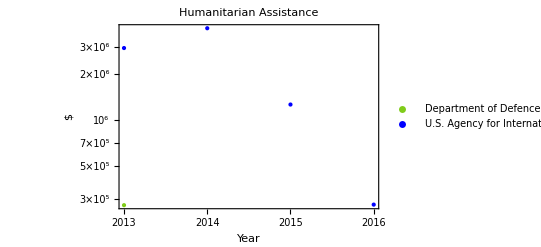

```mathematica
Show[lpDefenseCountry["Humanitarian Assistance","Tanzania"],lpInternDevelopCountry["Humanitarian Assistance","Tanzania"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}]
```

### Health*

```mathematica
dtotlistCountryNew["Health","Tanzania"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Health","Tanzania"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
2.4197416e7 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
3.7784235e7 $
2013
1.3140753900000001e6 $ | 2014
1.39041108e6 $ | 2015
1.52283008e6 $ | 2016
1.776064e6 $
2013
1.7610615159e8 $ | 2014
2.0225530842000002e8 $ | 2015
2.7521351493e8 $ | 2016
1.7237380178e8 $
2013
1.84021748e6 $ | 2014
4.29826501e6 $ | 2015
2.50998016e6 $ | 2016
1.7073810799999998e6 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
1.7412878259999998e7 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
-5.159044e6 $ | 2014
-5.96444925e6 $ | 2015
0.00 $ | 2016
0.00 $
2013
2.2887320196e8 $ | 2014
1.5667223824e8 $ | 2015
1.3141952477e8 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Health","Tanzania"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

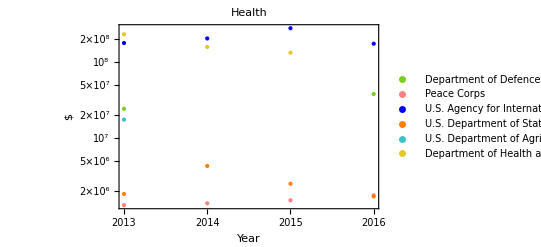

```mathematica
Show[lpDefenseCountry["Health","Tanzania"],lpPeaceCountry["Health","Tanzania"],lpInternDevelopCountry["Health","Tanzania"],lpDepartStateCountry["Health","Tanzania"],lpAgricultureCountry["Health","Tanzania"],lpHumanServicesCountry["Health","Tanzania"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}](*lpMillenniumnCountry["Health","Tanzania"]*)
```

### Environment*

```mathematica
dtotlistCountryNew["Environment","Tanzania"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Environment","Tanzania"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
164 896.56 $ | 2014
97 872.20 $ | 2015
3.02373268e6 $ | 2016
0.00 $
2013
5.60779624e6 $ | 2014
5.77541446e6 $ | 2015
9.540026e6 $ | 2016
8.00564966e6 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
295 629.50 $ | 2016
233 392.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Environment","Tanzania"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

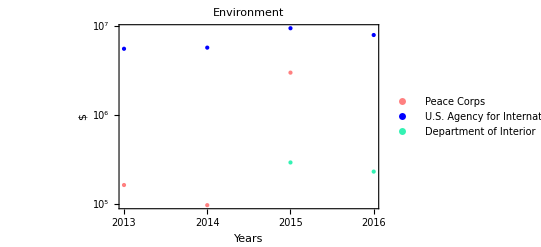

```mathematica
Show[lpPeaceCountry["Environment","Tanzania"],lpInternDevelopCountry["Environment","Tanzania"],lpInteriorCountry["Environment","Tanzania"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}]
```

## Ethiopia - Data (2013 - 2016) - categories

```mathematica
TableForm[DeleteDuplicates[datasetAll201316d1[[All,"Category"]]]]
```

Economic Development
Peace and Security
Program Management
Multi-sector
Education and Social Services
Democracy, Human Rights, and Governance
Humanitarian Assistance
Health
Environment

### Economic Development*

```mathematica
dtotlistCountryNew["Economic Development","Ethiopia"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Economic Development","Ethiopia"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
180 904.52 $ | 2014
304 983.97 $ | 2015
415 166.61 $ | 2016
77 201.00 $
2013
5.926095607000001e7 $ | 2014
6.543036654e7 $ | 2015
5.858054692e7 $ | 2016
4.4639296879999995e7 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
26 965.50 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
15 136.00 $ | 2014
342 727.00 $ | 2015
225 000.00 $ | 2016
655 000.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
2.384256e7 $ | 2014
3.759256e7 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Economic Development","Ethiopia"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

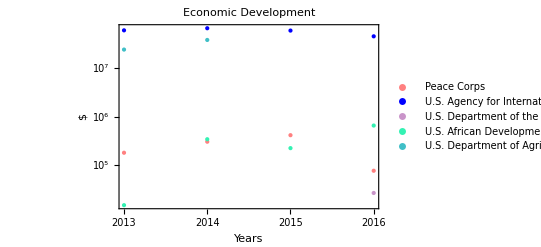

```mathematica
Show[lpPeaceCountry["Economic Development","Ethiopia"],lpInternDevelopCountry["Economic Development","Ethiopia"],lpTreasuryCountry["Economic Development","Ethiopia"],lpAfricaCountry["Economic Development","Ethiopia"],lpAgricultureCountry["Economic Development","Ethiopia"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2003,Log[5*10^3]}]
```

### Peace and Security*

```mathematica
dtotlistCountryNew["Peace and Security","Ethiopia"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Peace and Security","Ethiopia"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
75 000.00 $ | 2015
3.487016870999999e7 $ | 2016
3 000.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
2.4593228899999997e6 $ | 2014
1.4868214500000002e6 $ | 2015
1.148212e6 $ | 2016
1.943656e6 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Peace and Security","Ethiopia"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

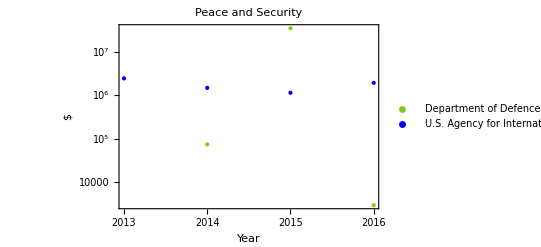

```mathematica
Show[lpDefenseCountry["Peace and Security","Ethiopia"],lpInternDevelopCountry["Peace and Security","Ethiopia"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}]
```

### Program Management*

```mathematica
dtotlistCountryNew["Program Management","Ethiopia"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Program Management","Ethiopia"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
1.0747907939999998e7 $ | 2014
1.156351119e7 $ | 2015
1.5927655930000002e7 $ | 2016
1.557969907e7 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
110 690.42 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
140 398.00 $ | 2016
112 563.07 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Program Management","Ethiopia"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

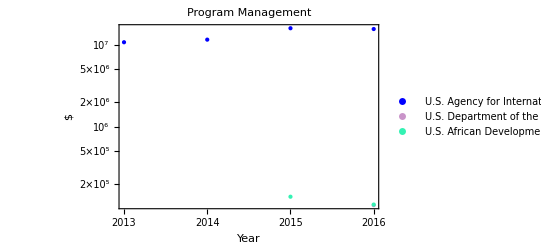

```mathematica
Show[lpInternDevelopCountry["Program Management","Ethiopia"],lpTreasuryCountry["Program Management","Ethiopia"],lpAfricaCountry["Program Management","Ethiopia"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}](*lpMillenniumnCountry["Program Management","Tanzania"]*)
```

### Multi-sector*

```mathematica
dtotlistCountryNew["Multi-sector","Ethiopia"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Multi-sector","Ethiopia"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
15 339.60 $ | 2014
15 597.25 $ | 2015
8 507.87 $ | 2016
8 036.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
30 821.67 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Multi-sector","Ethiopia"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

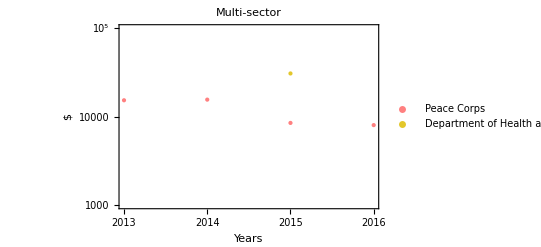

```mathematica
Show[lpPeaceCountry["Multi-sector","Ethiopia"],lpHumanServicesCountry["Multi-sector","Ethiopia"],PlotRange->{{2013,2016},{Log[10^3],Log[10^5]}},AxesOrigin->{2009,Log[5*10^2]}]
```

### Education and Social Services*

```mathematica
dtotlistCountryNew["Education and Social Services","Ethiopia"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Education and Social Services","Ethiopia"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
1.7806850699999998e6 $ | 2014
2.2242033899999997e6 $ | 2015
0.00 $ | 2016
2.858948e6 $
2013
5.339012141e7 $ | 2014
5.3990309760000005e7 $ | 2015
4.642502220999999e7 $ | 2016
4.734255409e7 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
25 987.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
2.6525e7 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Education and Social Services","Ethiopia"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

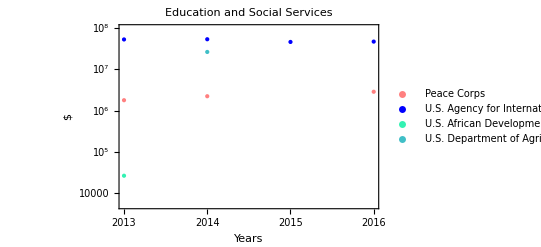

```mathematica
Show[lpPeaceCountry["Education and Social Services","Ethiopia"],lpInternDevelopCountry["Education and Social Services","Ethiopia"],lpAfricaCountry["Education and Social Services","Ethiopia"],lpAgricultureCountry["Education and Social Services","Ethiopia"],PlotRange->{{2013,2016},{Log[5*10^3],Log[10^8]}},AxesOrigin->{2009,Log[8*10^1]}]
```

### Democracy, Human Rights, and Governance*

```mathematica
dtotlistCountryNew["Democracy, Human Rights, and Governance","Ethiopia"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Democracy, Human Rights, and Governance","Ethiopia"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
-1.40033151e6 $ | 2014
694 522.61 $ | 2015
1.6605870699999998e6 $ | 2016
90 779.83 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Democracy, Human Rights, and Governance","Ethiopia"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

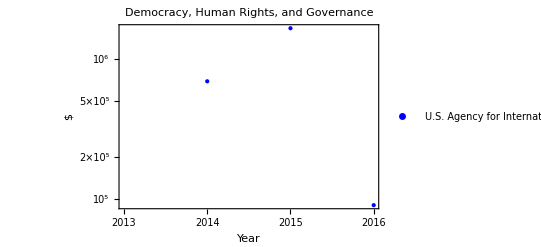

```mathematica
Show[lpInternDevelopCountry["Democracy, Human Rights, and Governance","Ethiopia"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}]
```

### Humanitarian Assistance*

```mathematica
dtotlistCountryNew["Humanitarian Assistance","Ethiopia"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Humanitarian Assistance","Ethiopia"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
1.4120416412e8 $ | 2014
2.1519033516e8 $ | 2015
2.1031364757e8 $ | 2016
5.0245888216999996e8 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Humanitarian Assistance","Ethiopia"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

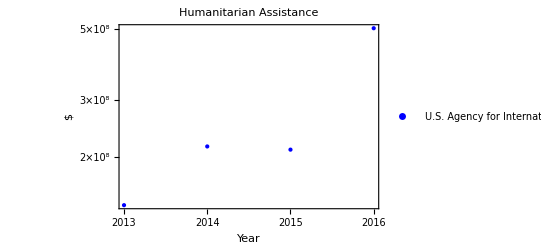

```mathematica
Show[lpInternDevelopCountry["Humanitarian Assistance","Ethiopia"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}]
```

### Health*

```mathematica
dtotlistCountryNew["Health","Ethiopia"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Health","Ethiopia"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
1.589136e6 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
194 506.00 $
2013
1.0062541200000001e6 $ | 2014
1.1020991099999999e6 $ | 2015
1.12413419e6 $ | 2016
1.104311e6 $
2013
2.1366487667000002e8 $ | 2014
2.0463297926000002e8 $ | 2015
2.1941983692000002e8 $ | 2016
2.1290656524e8 $
2013
7.474678350000001e6 $ | 2014
6.9998294e6 $ | 2015
3.72886801e6 $ | 2016
491 360.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
2.65e7 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
8.319559062e7 $ | 2014
5.863132006e7 $ | 2015
8.838042442e7 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Health","Ethiopia"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

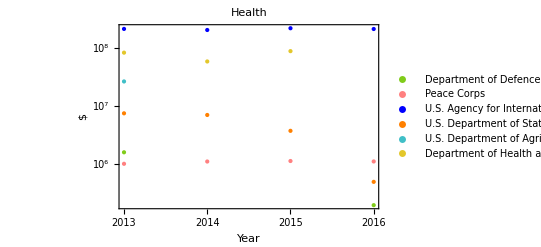

```mathematica
Show[lpDefenseCountry["Health","Ethiopia"],lpPeaceCountry["Health","Ethiopia"],lpInternDevelopCountry["Health","Ethiopia"],lpDepartStateCountry["Health","Ethiopia"],lpAgricultureCountry["Health","Ethiopia"],lpHumanServicesCountry["Health","Ethiopia"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}](*lpMillenniumnCountry["Health","Tanzania"]*)
```

### Environment*

```mathematica
dtotlistCountryNew["Environment","Ethiopia"]//TableForm;
```

```mathematica
Values[dtotlistCountryNew["Environment","Ethiopia"]]//TableForm
```

2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
578 665.61 $ | 2014
580 270.11 $ | 2015
3.4608095900000003e6 $ | 2016
1.288594e6 $
2013
2.0330276240000002e7 $ | 2014
2.2163256e7 $ | 2015
3.088449871e7 $ | 2016
4.1801496199999996e6 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
24 970.00 $ | 2016
62 243.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $
2013
0.00 $ | 2014
0.00 $ | 2015
0.00 $ | 2016
0.00 $

```mathematica
Keys[dtotlistCountryNew["Environment","Ethiopia"]][[All,1]]//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture
Millennium Challenge Corporation
Department of Health and Human Services

```mathematica
(*Show[lpOverseasCountry["Economic Development","Peru"],lpDefenseCountry["Economic Development","Peru"],lpPeaceCountry["Economic Development","Peru"],lpInternDevelopCountry["Economic Development","Peru"],lpDepartStateCountry["Economic Development","Peru"],lpTreasuryCountry["Economic Development","Peru"],lpInterAmericanCountry["Economic Development","Peru"],lpInteriorCountry["Economic Development","Peru"],lpAfricaCountry["Economic Development","Peru"],lpJusticeCountry["Economic Development","Peru"],lpLaborCountry["Economic Development","Peru"],lpAgricultureCountry["Economic Development","Peru"],lpMillenniumnCountry["Economic Development","Peru"],lpHumanServicesCountry["Economic Development","Peru"],PlotRange->{{2014,2017},{Log[5*10^3],Log[5*10^6]}}]*)
```

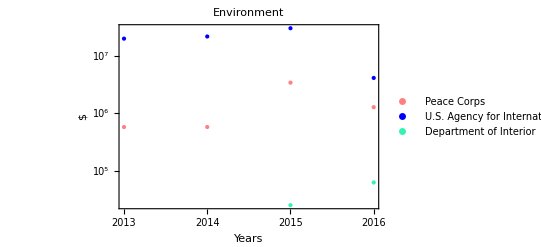

```mathematica
Show[lpPeaceCountry["Environment","Ethiopia"],lpInternDevelopCountry["Environment","Ethiopia"],lpInteriorCountry["Environment","Ethiopia"],PlotRange->{{2013,2016},{All,All}},AxesOrigin->{2009,Log[5*10^3]}](*ImageSize->Large*)
```